# Analytical solutions for simple cases

First let us assume is small i.e.,  
and using geometric series expansion . 
We also assume that 
 
as a quadratic geometry. Thus the resulting ODE is:

The ODE is of the form: 
where 
 
.
The solution is

```mathematica
(*Define parameters as symbolic*)
ClearAll[H,H0,x,α](*α -> Tan[θ]*)
P[x_]:=Subscript[b, 0] (α-2 Subscript[b, 0] x (1+α^2))
Q[x_]:=-Subscript[f, λ]+α-4 Subscript[b, 0] x (1+α^2)
(*Solve the ODE symbolically*)
solH=DSolve[{H'[x]+P[x] H[x]==Q[x],H[0]==H0},H[x],{x,-1,1}];
Hanalytical = H[x]/.solH[[1]]
Happrox = Normal[Series[Hanalytical,{x,0,2}]]
```

1/(2 √(1+α^2) b_0)ⅇ^(-x b_0 (α-x (1+α^2) b_0)) (-4 √(1+α^2)+4 ⅇ^(x b_0 (α-x (1+α^2) b_0)) √(1+α^2)-ⅇ^(α^2/(4+4 α^2)) √π α Erf[α/(2 √(1+α^2))]-ⅇ^(α^2/(4+4 α^2)) √π α Erf[(-α+2 x (1+α^2) b_0)/(2 √(1+α^2))]+2 H0 √(1+α^2) b_0-ⅇ^(α^2/(4+4 α^2)) √π (Erf[α/(2 √(1+α^2))]+Erf[(-α+2 x (1+α^2) b_0)/(2 √(1+α^2))]) f_λ)

H0+x (α-H0 α b_0-f_λ)+1/2 x^2 b_0 (-4-5 α^2+2 H0 b_0+3 H0 α^2 b_0+α f_λ)

NDSolve::ndsz: At x == -0.476998, step size is effectively zero; singularity or stiff system suspected.

NDSolve::ndsz: At x == 0.922661, step size is effectively zero; singularity or stiff system suspected.

InterpolatingFunction::dmval: Input value {-0.999959} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {-0.959143} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {-0.918326} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

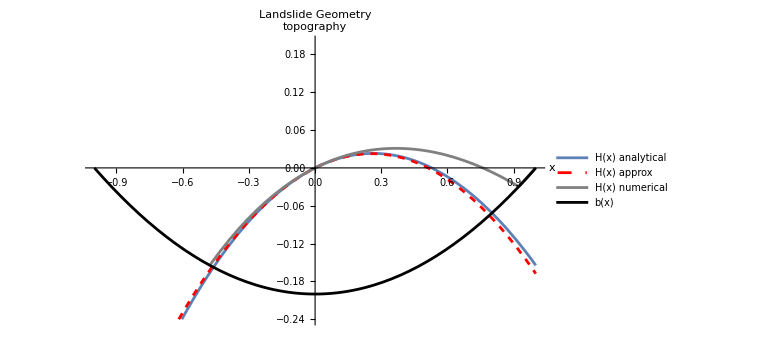

InterpolatingFunction::dmval: Input value {-0.999959} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {-0.959143} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {-0.918326} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

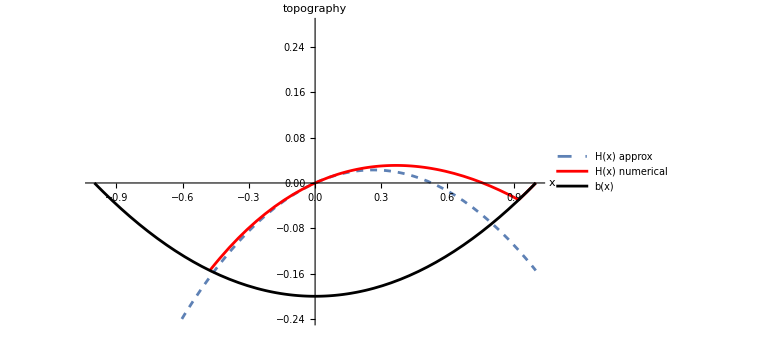

/Users/mallickrishg/Documents/GitHub/landslides/analyticsol/AnalyticalSolutionProfile.jpg

```mathematica
(*Define H[x]*)
H0 = 0.2;
bmax=H0;
bv = bmax*(x^2-1);
αv = 0.6;
fv=0.4;

eqnlogODE = -Exp[ϕ[x]]*D[ϕ[x],x] - 0.5*(αv-D[bv,x])/(1+(D[bv,x])^2)*D[bv,x,x]/(1+D[bv,x]*αv)*Exp[ϕ[x]] == fv+D[bv,x] -(αv-D[bv,x])/(1+D[bv,x]*αv);
sollogss = NDSolve[{eqnlogODE,ϕ[0]==Log[H0]},ϕ,{x,-1,1}];
Hnumeric =  Exp[ϕ[x]/.sollogss];

(*Plot results and comparisons*)
p1=Plot[{bv+Hanalytical/.{H0->H0,Subscript[b, 0]->bmax,α->αv,Subscript[f, λ]->fv},bv+Happrox/.{H0->H0,Subscript[b, 0]->bmax,α->αv,Subscript[f, λ]->fv},Hnumeric+bv,bv},{x,-1,1},PlotStyle->{DarkBlue,{Red,Dashed},{Gray},Black},PlotLabel->"Landslide Geometry",AxesLabel->{"x","topography"},PlotLegends->{"H(x) analytical","H(x) approx","H(x) numerical","b(x)"},ImageSize->Large,PlotRange->{-1.2*bmax,bmax}]
p1=Plot[{bv+Hanalytical/.{H0->H0,Subscript[b, 0]->bmax,α->αv,Subscript[f, λ]->fv},Hnumeric+bv,bv},{x,-1,1},PlotStyle->{{DarkBlue,Dashed,Thick},{Red},Black},AxesLabel->{"x","topography"},PlotLegends->{"H(x) approx","H(x) numerical","b(x)"},ImageSize->Large,PlotRange->{-1.2*bmax,1.4*bmax},LabelStyle->{FontSize->20}]
Export[NotebookDirectory[]<>"AnalyticalSolutionProfile.jpg",p1,"JPEG",ImageResolution->500]
```

```mathematica
b = b0*(x^2-1);
eqnice=Subscript[f, λ]+ρ*α-(α-D[b,x])/(1+D[b,x]* α)==
(ρ-1)*(H'[x]+D[b,x])+
-((α-D[b,x])/(1+(D[b,x])^2))*(D[b,x,x]/(1+D[b,x] α))*(H[x]/2)+
-(ρ)*((H0-b)-H[x]+x*α)*(Subscript[f, λ]/H[x]+D[b,x,x]*((α/(1+D[b,x] α))-D[b,x]/(1+(D[b,x])^2)));
eqnb0=Simplify[eqnice/. {(D[b,x])^2->0,1+(D[b,x])^2->1}];
dummy=eqnb0/. 1/(1+2 b0 x α)->Normal[Series[1/(1+2 b0 x α),{b0,0,1}]]
(*Simplify equation by assuming small b0*)
dummy=Collect[dummy,b0]/.{b0^3->0,b0^2->0,1/H[x]->1/H0 - (H[x]-H0)/(H0^2)};
dummysol=DSolve[{dummy,H[0]==H0},H[x],{x,-1,1}];
Hiceanalytic=Normal[Series[H[x]/.dummysol[[1]],{x,0,2}]]

(*eqnb0=Normal[Series[eqnicemod,{b0,0,1}]];
eqnb0mod = -α+2 b0 (x+x α^2)+α ρ+Subscript[f, λ]==-ρ (H0+x α-H[x]) Subscript[f, λ]*(1/H0-(H[x]-H0)/H0^2)+b0 (2 x (-1+ρ)-α H[x]+ρ (-2 α (H0+x α-H[x])-(1-x^2) Subscript[f, λ]*(1/H0-(H[x]-H0)/H0^2)))+(-1+ρ) H'[x]
DSolve[{eqnb0,H[0]==H0},H[x],{x,-1,1}]*)
```

(2 b0 x-α) (1-2 b0 x α)+α ρ+f_λ+ρ (b0+H0-b0 x^2+x α-H[x]) (2 b0 (-2 b0 x+α (1-2 b0 x α))+f_λ/H[x])==b0 (2 b0 x-α) (1-2 b0 x α) H[x]+(-1+ρ) (2 b0 x+H'[x])

H0+(x (-H0 α+b0 H0^2 α+H0 α ρ+H0 f_λ+b0 ρ f_λ))/(H0 (-1+ρ))+1/(2 H0^3 (-1+ρ)^2)x^2 (-4 b0 H0^3-3 b0 H0^3 α^2+b0^2 H0^4 α^2+6 b0 H0^3 ρ+3 b0 H0^3 α^2 ρ-2 b0^2 H0^4 α^2 ρ-2 b0 H0^3 ρ^2+b0 H0^3 α f_λ+b0 H0 α ρ f_λ-3 b0 H0^3 α ρ f_λ-b0 H0 α ρ^2 f_λ-2 b0^2 H0^2 α ρ^2 f_λ-b0 H0 ρ f_λ^2-H0^2 ρ f_λ^2-b0^2 ρ^2 f_λ^2-b0 H0 ρ^2 f_λ^2)

```mathematica
Hiceanalytic/.{b0^2->0}
```

H0+(x (-H0 α+b0 H0^2 α+H0 α ρ+H0 f_λ+b0 ρ f_λ))/(H0 (-1+ρ))+1/(2 H0^3 (-1+ρ)^2)x^2 (-4 b0 H0^3-3 b0 H0^3 α^2+6 b0 H0^3 ρ+3 b0 H0^3 α^2 ρ-2 b0 H0^3 ρ^2+b0 H0^3 α f_λ+b0 H0 α ρ f_λ-3 b0 H0^3 α ρ f_λ-b0 H0 α ρ^2 f_λ-b0 H0 ρ f_λ^2-H0^2 ρ f_λ^2-b0 H0 ρ^2 f_λ^2)